## Woods-Saxon potential

```mathematica
vws[r_,V0_,R0_,s_]:=-V0/(1+Exp[(r-R0)/s]);
woods[r_]:=vws[r,v0,r0,s0];
```

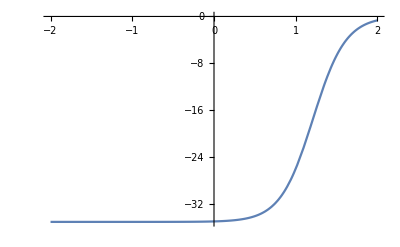

```mathematica
v0=35;
s0=0.2;
r0=1.21;
Plot[woods[r],{r,-2,2}]
```